```mathematica
Solve[x+α==α*Exp[x*t],t]
```

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[(x+α)/α])/x,C[1]∈Integers]}}

```mathematica
1/X * Log[(X+α)/α]/.{X->(.7-.8+.3),α->.3}
```

2.55413

```mathematica
Manipulate[
ContourPlot[
1/(bR-bS+α)* Log[((bR-bS+α)+α)/α],
{α,.01,.1},{bR,.7,.8},
AxesLabel->Automatic
],
{{bS,.8},.1,0.8}
]
```

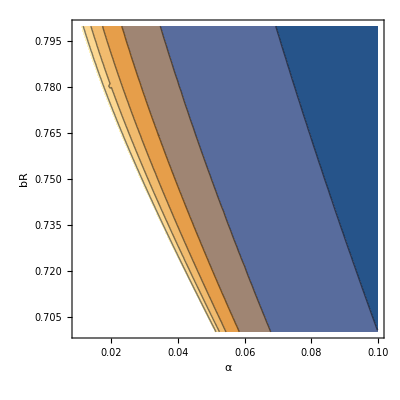

```mathematica
ContourPlot[
1/(bR-bS+α)* Log[((bR-bS+α)+α)/α]/.bS->.8,
{α,.01,.1},{bR,.7,.8},
AxesLabel->Automatic
]
```

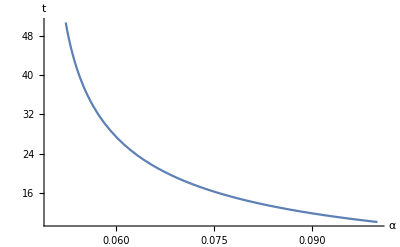

```mathematica
Plot[1/(bR-bS+α)* Log[((bR-bS+α)+α)/α]/.{bS->.8,bR->.7},
{α,.05,.1},
AxesLabel->{"α","t"}]
```